```mathematica
ti=0;tf=1;
s=NDSolve[{
x1'[t]==1/2*x1[t]+u[t],
x2'[t]==x1[t]*u[t]+5/4*(x1[t])^2+(u[t])^2,
λ1'[t]==-1/2*λ1[t]-(u[t]+5/2*x1[t])*λ2[t],
λ2'[t]==0,
λ1[t]+λ2[t]*(x1[t]+2*u[t])==0,
λ1[ti]==0,
λ2[ti]==0,
λ1[tf]==ν1, 
λ2[tf]==ν2+1,
x1[tf]-1==0,
x2[tf]==0,
(x1[tf]*u[tf]+5/4*x1[tf]^2+u[tf]^2)*(ν2+1)+(1/2 x1[tf]+u[tf])*ν1==0
},{x1,x2,λ1,λ2,u,ν1,ν2},{t,ti,tf}]
```

NDSolve::bvdae: Differential-algebraic equations must be given as initial value problems.

NDSolve[{x1'[t]==u[t]+x1[t]/2,x2'[t]==u[t]^2+u[t] x1[t]+(5 x1[t]^2)/4,λ1'[t]==-λ1[t]/2-(u[t]+(5 x1[t])/2) λ2[t],λ2'[t]==0,λ1[t]+(2 u[t]+x1[t]) λ2[t]==0,λ1[0]==0,λ2[0]==0,λ1[1]==ν1,λ2[1]==1+ν2,-1+x1[1]==0,x2[1]==0,ν1 (u[1]+x1[1]/2)+(1+ν2) (u[1]^2+u[1] x1[1]+(5 x1[1]^2)/4)==0},{x1,x2,λ1,λ2,u,ν1,ν2},{t,0,1}]

```mathematica
ti=0;tf=1;
s=NDSolve[{
x1'[t]==1/2*x1[t]+u[t],
x2'[t]==x1[t]*u[t]+5/4*(x1[t])^2+(u[t])^2,
λ1'[t]==-1/2*λ1[t]-(u[t]+5/2*x1[t])*λ2[t],
λ2'[t]==0,
λ1[t]+λ2[t]*(x1[t]+2*u[t])==0,
λ1[ti]==0,
λ2[ti]==0,
x1[ti]-1==0,
x2[ti]==0
},{x1,x2,λ1,λ2,u},{t,ti,tf}]
```

NDSolve::indexss: The DAE solver failed at t = 0.. The solver is intended for index 1 DAE systems and structural analysis indicates that the DAE is structurally singular.

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…],λ1→InterpolatingFunction[…],λ2→InterpolatingFunction[…],u→InterpolatingFunction[…]}}

```mathematica
x1r[t_]:=Cosh[1-t]/Cosh[1];
ur[t_]:=(-(Tanh[1-t]+0.5)*Cosh[1-t])/Cosh[1]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

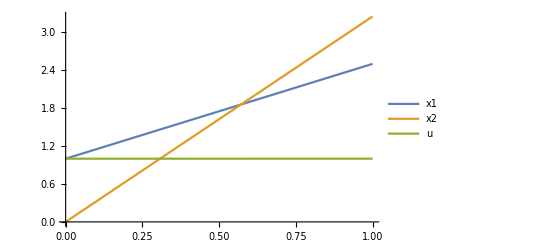

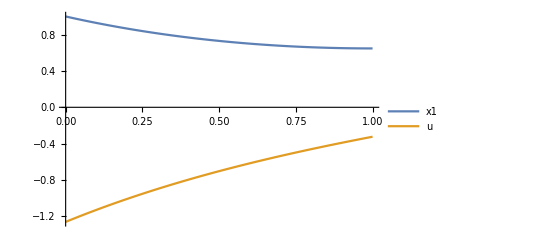

```mathematica
Plot[Evaluate[{x1[t],x2[t],u[t]}/.s],{t,0,1},PlotStyle->Automatic,PlotLegends->{"x1","x2","u"}]
Plot[{x1r[t],ur[t]},{t,0,1},PlotStyle->Automatic,PlotLegends->{"x1","u"}]
```